```mathematica
ClearAll["Global`*"]
wd=SetDirectory@NotebookDirectory[];
hydroPath = "/../../output";
exactPath = "/../../semi_analytic";
```

```mathematica
order=2;

eExactdata=Import[wd<>exactPath<>"/e_e0_aniso_bjorken.dat"];
plptExactdata=Import[wd<>exactPath<>"/pl_pt_aniso_bjorken.dat"];
eExact=Interpolation[eExactdata];
plptExact=Interpolation[plptExactdata];
t0=eExactdata[[1,1]];
tfExact=eExactdata[[-1,1]]

eVAHdata=Import[wd<>hydroPath<>"/eratio.dat"];
plptVAHdata=Import[wd<>hydroPath<>"/plptratio.dat"];
tfVAH=eVAHdata[[-1,1]]

eVAH=Interpolation[eVAHdata];
plptVAH=Interpolation[plptVAHdata];


de=eVAHdata[[1;;(Length[eVAHdata]-1)]];
de[[All,2]]/=eExact[de[[All,1]]];
de=Interpolation[de,InterpolationOrder->order];

dplpt=plptVAHdata[[1;;(Length[plptVAHdata]-1)]];
dplpt[[All,2]]/=plptExact[dplpt[[All,1]]];
dplpt=Interpolation[dplpt,InterpolationOrder->order];

tf=Min[tfExact,tfVAH]

Print["Length of hydro data = ", Length[eVAHdata]]
Print["Length of exact data = ",Length[eExactdata]]
```

24.7433

24.9209

24.7433

Length of hydro data = 286

Length of exact data = 247334

```mathematica
redTran={Red,AbsoluteThickness[2],Opacity[0.3]};
red={Red,AbsoluteDashing[{8,6}],AbsoluteThickness[2]};
redSolid={Red,AbsoluteThickness[1.5]};

blackSolid={Black,AbsoluteThickness[1.5]};
gray={RGBColor[0.4,0.4,0.4],AbsoluteThickness[1.25]};

min = {0.009,0};
maj={0.016,0};

logticks = {{0.00001,"10^-5",maj},{0.00002,"",min},{0.00003,"",min},{0.00004,"",min},{0.00005,"",min},{0.00006,"",min},{0.00007,"",min},{0.00008,"",min},{0.00009,"",min},{0.0001,"10^-4",maj},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"10^-3",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"0.01",maj},
{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,0.1,maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1,"1.0",maj}};

nologticks = {{0.00001,"",maj},{0.00002,"",min},{0.00003,"",min},{0.00004,"",min},{0.00005,"",min},{0.00006,"",min},{0.00007,"",min},{0.00008,"",min},{0.00009,"",min},{0.0001,"",maj},{0.0002,"",min},{0.0003,"",min},{0.0004,"",min},{0.0005,"",min},{0.0006,"",min},{0.0007,"",min},{0.0008,"",min},{0.0009,"",min},{0.001,"",maj},{0.002,"",min},{0.003,"",min},{0.004,"",min},{0.005,"",min},{0.006,"",min},{0.007,"",min},{0.008,"",min},{0.009,"",min},{0.01,"",maj},
{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1,"",maj}};

Tticks = {{0.1,"0.1",maj},{0.125,"",min},{0.15,"",min},{0.175,"",min},{0.2,"0.2",maj},{0.225,"",min},{0.25,"",min},{0.275,"",min},{0.3,"0.3",maj},{0.325,"",min},{0.35,"",min},{0.375,"",min},{0.4,"0.4",maj},{0.425,"",min},{0.45,"",min},{0.475,"",min},{0.5,"0.5",maj},{0.525,"",min},{0.55,"",min},{0.575,"",min},{0.6,"0.6",maj},{0.625,"",min},{0.65,"",min}};

Tnoticks = {{0.1,"",maj},{0.125,"",min},{0.15,"",min},{0.175,"",min},{0.2,"",maj},{0.225,"",min},{0.25,"",min},{0.275,"",min},{0.3,"",maj},{0.325,"",min},{0.35,"",min},{0.375,"",min},{0.4,"",maj},{0.425,"",min},{0.45,"",min},{0.475,"",min},{0.5,"",maj},{0.525,"",min},{0.55,"",min},{0.575,"",min},{0.6,"",maj},{0.625,"",min},{0.65,"",min}};

plptticks = {{0,"0.0",maj},{0.05,"",min},{0.1,"",min},{0.15,"",min},{0.2,"0.2",maj},{0.25,"",min},{0.3,"",min},{0.35,"",min},{0.4,"0.4",maj},{0.45,"",min},{0.5,"",min},{0.55,"",min},{0.6,"0.6",maj},{0.65,"",min},{0.7,"",min},{0.75,"",min},{0.8,"0.8",maj},{0.85,"",min},{0.9,"",min},{0.95,"",min},{1.0,"1.0",maj},{1.05,"",min}};

plptnoticks = {{0,"",maj},{0.05,"",min},{0.1,"",min},{0.15,"",min},{0.2,"",maj},{0.25,"",min},{0.3,"",min},{0.35,"",min},{0.4,"",maj},{0.45,"",min},{0.5,"",min},{0.55,"",min},{0.6,"",maj},{0.65,"",min},{0.7,"",min},{0.75,"",min},{0.8,"",maj},{0.85,"",min},{0.9,"",min},{0.95,"",min},{1.0,"",maj},{1.05,"",min}};


timeticks = {{0.01,"0.01",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"0.1",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"1.0",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"10",maj},{20,"",min}};

notimeticks = {{0.01,"",maj},{0.02,"",min},{0.03,"",min},{0.04,"",min},{0.05,"",min},{0.06,"",min},{0.07,"",min},{0.08,"",min},{0.09,"",min},{0.1,"",maj},{0.2,"",min},{0.3,"",min},{0.4,"",min},{0.5,"",min},{0.6,"",min},{0.7,"",min},{0.8,"",min},{0.9,"",min},{1.0,"",maj},{2,"",min},{3,"",min},{4,"",min},{5,"",min},{6,"",min},{7,"",min},{8,"",min},{9,"",min},{10,"",maj},{20,"",min}};

ratioticks = {{0.995,"0.995",maj},{0.996,"",min},{0.997,"",min},{0.998,"",min},{0.999,"",min},{1,"1.0",maj},
{1.001,"",min},{1.002,"",min},{1.003,"",min},{1.004,"",min},{1.0050,"1.005",maj}};

noratioticks = {{0.995,"",maj},{0.996,"",min},{0.997,"",min},{0.998,"",min},{0.999,"",min},{1,"",maj},
{1.001,"",min},{1.002,"",min},{1.003,"",min},{1.004,"",min},{1.005,"",maj}};

eLabel=Panel[Grid[{{Style["(ℰ_(<>))/ℰ_0",FontSize->26,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
eFS=Panel[Grid[{{Style["τ_0/τ",FontSize->18,FontFamily->"Arial",RGBColor[0.4,0.4,0.4]]}}],Background->White,FrameMargins->0];
eIdeal=Panel[Grid[{{Style["(τ_0/τ)^(4/3)",FontSize->18,FontFamily->"Arial",RGBColor[0.4,0.4,0.4]]}}],Background->White,FrameMargins->0];
plpt=Panel[Grid[{{Style["(P_(L_((<>)_(<>))))/(P_⊥)",FontSize->26,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];

initTime=Panel[Grid[{{Style["τ_0 = 0.01 fm/c",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
initTemp=Panel[Grid[{{Style["T_0 = 1.35 GeV",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
initPLPT=Panel[Grid[{{Style["P_L0/P_(⊥0) = 10^-3",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];



legend1=Panel[Grid[{{Graphics[{Directive[RGBColor[1,0,0.1],AbsoluteDashing[{8,6}],AbsoluteThickness[2.5]],Line[{{0,0},{1,0}}]},ImageSize->38,AspectRatio->0.5],Style["CPU VAH",FontSize->14,FontFamily->"Arial"]},
{Graphics[{Directive[Red,Opacity[0.3],AbsoluteThickness[2.5]],Line[{{0,0},{1,0}}]},ImageSize->38,AspectRatio->0.5],Style["Semi-analytic",FontSize->14,FontFamily->"Arial"]}}],Background->White,FrameMargins->0];

eRatioLabel=Panel[Grid[{{Style["(ℰ_((<>)_(<>)))/ℰ_exact",FontSize->22,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
plptRatioLabel=Panel[Grid[{{Style["(P_(L_((<>)_(<>))))/((SubscriptBox[P, L]/SubscriptBox[P, ⊥])_exact)",FontSize->22,FontFamily->"Arial",Black]}}],Background->White,FrameMargins->0];
```

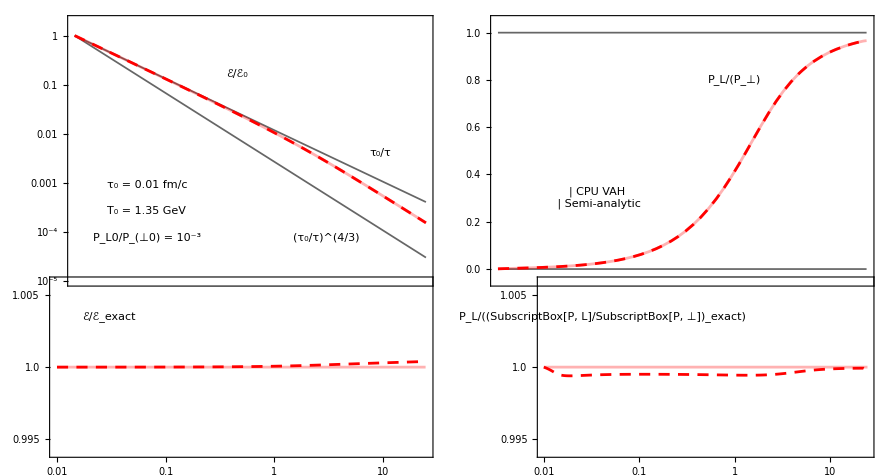
-Graphics-τ (fm/c)

```mathematica
a=37;
b=a;

image=450;

plot1=LogLogPlot[{(t0/t)^(4/3),t0/t,eExact[t],eVAH[t]},{t,t0,tf}, PlotRange->{{t0,tf},{10^-5,2}},Frame->True,FrameTicks->{{logticks,nologticks},{notimeticks,notimeticks}},PlotStyle->{gray,gray,redTran,red},FrameStyle->Black,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.75,ImageSize->450,ImagePadding->{{a,b},{Automatic,Automatic}},Epilog->{Inset[eLabel,{-1,-1.8}],Inset[eFS,{2.2,-5.5}],Inset[eIdeal,{1,-9.5}],Inset[initTime,{-3,-7.}],Inset[initTemp,{-3,-8.25}],Inset[initPLPT,{-3,-9.5}]}];

plot2 = LogLinearPlot[{0,1,plptExact[t],plptVAH[t]},{t,t0,tf},  PlotRange->{{t0,tf},{-0.05,1.05}},Frame->True,FrameTicks->{{plptticks,plptnoticks},{notimeticks,notimeticks}},PlotStyle->{gray,gray,redTran,red},FrameStyle->Black,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.75,ImageSize->450,ImagePadding->{{a,b},{Automatic,Automatic}},Epilog->{Inset[plpt,{0.4,0.8}],Inset[legend1,{-2.5,0.3}]}];

plot3=LogLinearPlot[{1,de[t]},{t,t0,tf},PlotRange->{{t0,tf},{0.994,1.006}},PlotStyle->{redTran,red},Frame->True,FrameTicks->{{ratioticks,noratioticks},{timeticks,notimeticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.5,ImagePadding->{{a,b},{Automatic,Automatic}},Epilog->{Inset[eRatioLabel,{-3.5,1.0035}]},ImageSize->image];

plot4=LogLinearPlot[{1,dplpt[t]},{t,t0,tf},PlotRange->{{t0,tf},{0.994,1.006}},PlotStyle->{redTran,red},Frame->True,FrameTicks->{{ratioticks,noratioticks},{timeticks,notimeticks}},FrameStyle->Black,Axes->None,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.5,ImagePadding->{{a,b},{Automatic,Automatic}},Epilog->{Inset[plptRatioLabel,{-3.2,1.0035}]},ImageSize->image];

plot=Panel[GraphicsGrid[{{plot1,plot2},{plot3,plot4}},Spacings->{-10,-106}],{Style["τ (fm/c)",FontFamily->"Arial",FontSize->16]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]
Export[wd<>"/bjorken_plot.png",plot];
Export[wd<>"/bjorken_plot.pdf",plot];
```

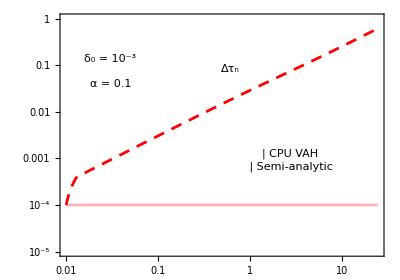
-Graphics-τ (fm/c)

```mathematica
adaptive=Interpolation[Import[wd<>hydroPath<>"/dt_adaptive.dat"]];

delta0=Panel[Grid[{{Style["δ_0 = 10^-3",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
alpha=Panel[Grid[{{Style["α = 0.1",FontSize->14,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];
dt=Panel[Grid[{{Style["Δτ_n",FontSize->18,FontFamily->"Arial",RGBColor[0,0,0]]}}],Background->White,FrameMargins->0];

timestep=LogLogPlot[{10^-4,adaptive[t]},{t,t0,tf},PlotRange->{{t0,tf},{10^-5,1}},Frame->True,FrameTicks->{{logticks,nologticks},{timeticks,notimeticks}},PlotStyle->{redTran,red},FrameStyle->Black,BaseStyle->{FontSize->13,FontFamily->"Arial"},AspectRatio->0.7,ImageSize->400,Epilog->{Inset[legend1,{1,-7}],Inset[dt,{-0.5,-2.5}],Inset[delta0,{-3.5,-2.}],Inset[alpha,{-3.5,-3.25}]}];

timeplot=Panel[GraphicsGrid[{{timestep}},Spacings->{0,0}],{Style["τ (fm/c)",FontFamily->"Arial",FontSize->16]},{{Bottom,Center}},Appearance->"Frameless",FrameMargins->0,Background->White]

Export[wd<>"/bjorken_adaptive.png",timeplot];
Export[wd<>"/bjorken_adaptive.pdf",timeplot];
```